```mathematica
Quit[]
```

```mathematica
"Units:"
"Time: years"
"Length: pc"
"Mass: Solar mass"
a:=20000(*20 000 pc = 20kpc*)
M:=10^12(*Solar masses*)
m:=4*10^6(*Solar masses*)
G:=4.49*10^-15(*pc^3/(solar mass * yr^2)*)
c:=0.3064(*pc/yr*)
Subscript[m, p]:=10^-3(*Solar mass *)
Rs:=2(G m)/c^2
```

Units:

Time: years

Length: pc

Mass: Solar mass

```mathematica
Quit[]
```

```mathematica
"Potential and 4-velocity"
Φ[r_]:=-(G M)/(a+r)
fourVelocity[ΕN_,L_]:=√(2 ΕN/Subscript[m, p]-2Φ[r]-(L/(Subscript[m, p] r))^2)
```

Potential and 4-velocity

```mathematica
"Conversion between relativistic and newtonian energy"
RelativisticToNewtonian[Ε_]:=Subscript[m, p]/2(Ε^2/(c^2 Subscript[m, p]^2)-c^2)
```

Conversion between relativistic and newtonian energy

```mathematica
"Roots of the equation (limits of integration)"
R1[ΕN_,L_]:=Root[-a L^2-L^2 #1+2 ΕN #1^3 Subscript[m, p]+#1^2 (2 a ΕN Subscript[m, p]+2 G M Subscript[m, p]^2)&,1]
R2[ΕN_,L_]:=Root[-a L^2-L^2 #1+2 ΕN #1^3 Subscript[m, p]+#1^2 (2 a ΕN Subscript[m, p]+2 G M Subscript[m, p]^2)&,2]
R3[ΕN_,L_]:=Root[-a L^2-L^2 #1+2 ΕN #1^3 Subscript[m, p]+#1^2 (2 a ΕN Subscript[m, p]+2 G M Subscript[m, p]^2)&,3]
radialAction[ΕN_,L_]:=NIntegrate[fourVelocity[ΕN,L],{r,R2[ΕN,L],R3[ΕN,L]}]
```

Roots of the equation (limits of integration)

Plot values

Plot values:

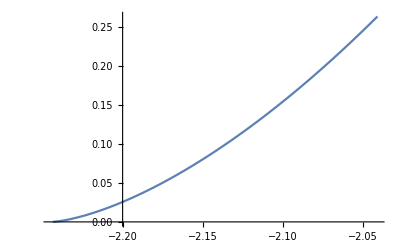

```mathematica
"Plot values"
"Plot values:"
Lmax:=1.5552632176183547*10^-7
Plot[radialAction[ΕN,Lmax*0.5],{ΕN,Φ[a]/500,Φ[a]/550}]
```

```mathematica
Lmax*0.5
radialAction[-2.1*10^-10,Lmax*0.5]
```

7.77632×10^-8

0.154553